# 相関円 （？）

```mathematica
cp[200]=CirclePoints[1,200];
```

```mathematica
Graphics[{PointSize[0.01],RGBColor[0.18,0.5,0.5],pt=Map[Point,cp[200]]}]
```

-Graphics-

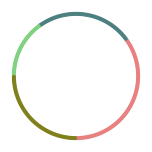

```mathematica
Graphics[ptGrp={RGBColor[0.91,0.5,0.5],pt[[1;;70]],RGBColor[0.3,0.5,0.5],pt[[71;;70+50]],RGBColor[0.5,0.82,0.5],pt[[70+50+1;;70+50+30]],RGBColor[0.5,0.5,0.11],pt[[70+50+30+1;;200]]}]
```

```mathematica
randomPair=Table[{RandomInteger[{1,200}],RandomInteger[{1,200}]},{70}];
```

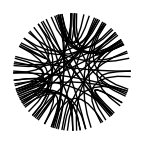

```mathematica
Graphics[bzpair=Map[BezierCurve[{cp[200][[#[[1]]]],{0,0},cp[200][[#[[2]]]]}]&,randomPair]]
```

```mathematica
Length[bzpair]
```

70

```mathematica
bzpairGrp={CMYKColor[0.0,0.3,0.0,0.1],bzpair[[1;;20]],CMYKColor[0.3,0.0,0.0,0.1],bzpair[[21;;20+15]],CMYKColor[0.0,0.0,0.3,0.1],bzpair[[20+15+1;;70]]};
```

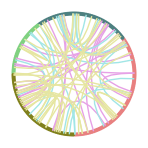

```mathematica
Graphics[{PointSize[0.02],ptGrp,bzpairGrp}]
```

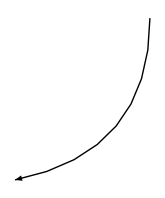

```mathematica
Graphics[{bzArr=Arrow[BezierCurve[{{1.2,0},{1.2,-1},{0.2,-1.2}}]]}]
```

```mathematica
tx01=Text["sort",{1,-1}]
```

Text[sort,{1,-1}]

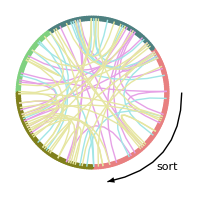

```mathematica
g0201=Graphics[{PointSize[0.02],ptGrp,bzpairGrp,RGBColor[0,0,0],bzArr,Style[tx01,14]},ImageSize->200]
```

```mathematica
Export["/Volumes/HFS/NII/CiNii/g02-01.jpg",g0201,ImageResolution->1200]
```

/Volumes/HFS/NII/CiNii/g02-01.jpg